```mathematica
(*more detailed analysis is in drops_blablabla*)
```

```mathematica
realklpt[k_,l_,a_,b_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,a,0],l==0}}]
```

```mathematica
bkl1fun[oh_,bo_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[c0,d0,m1k,m2k];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;gg=bo/wem;
rhoj=ρ1-ρ2;
fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
deltak=delta(μ1*(k-1)+μ2*(k+2))*fk;
zetak=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
(*m1k=If[Δk==0&&ζk==1,0,(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2)];*)
bkl0amp=plf=-(gg rhoj)/zetak^2+1/2 rhoj (-(6 deltak Cos[t])/(1+4 deltak^2-2 zetak^2+zetak^4)+(2 gg (-4+zetak^2) Cos[2 t])/(16 deltak^2+(-4+zetak^2)^2)+(6 deltak Cos[3 t])/(36 deltak^2+(-9+zetak^2)^2)+(3 (-1+zetak^2) Sin[t])/(1+4 deltak^2-2 zetak^2+zetak^4)+(8 deltak gg Sin[2 t])/(16 deltak^2+(-4+zetak^2)^2)-((-9+zetak^2) Sin[3 t])/(36 deltak^2+(-9+zetak^2)^2)))(*leading order amplitude of different modes at the resonance frequency kr*)
```

```mathematica
b201[s_]:=bkl1fun[ohn,bond,rho1,rho2,mu1,mu2,2,0,2,1]/.t->s;
b211[s_]:=c21*Cos[s]+d21*Sin[s]/.t->s;
b301[s_]:=bkl1fun[ohn,bond,rho1,rho2,mu1,mu2,3,0,2,1]/.t->s;
b401[s_]:=bkl1fun[ohn,bond,rho1,rho2,mu1,mu2,4,0,2,1]/.t->s;

etaa1[a_,b_,c_]:=b201[c]*realklpt[2,0,a,b]+b211[c]*realklpt[2,1,a,b]+b301[c]*realklpt[3,0,a,b]+b401[c]*realklpt[4,0,a,b]

fi11[rr_,a_,b_,c_]:=D[b201[c],c]/2*rr^1*realklpt[2,0,a,b]+D[b211[c],c]/2*rr^2*realklpt[2,1,a,b]+D[b301[c],c]/3*rr^3*realklpt[3,0,a,b]+D[b401[c],c]/4*rr^4*realklpt[4,0,a,b]

fi21[rr_,a_,b_,c_]:=-D[b201[c],c]/(2 rr^2)*realklpt[2,0,a,b]-D[b211[c],c]/(3 rr^3)*realklpt[2,1,a,b]-D[b301[c],c]/(4 rr^4)*realklpt[3,0,a,b]-D[b401[c],c]/(5 rr^5)*realklpt[4,0,a,b]
```

```mathematica
kkl1fun
```

```mathematica
kkl1fun=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]]} //Chop;
```

```mathematica
lkl1fun=η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} ;
```

```mathematica
nkl1fun=1/We(-2 (η1[θ,φ,t]^2)+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))+rho1 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])-1/2 rho2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} ;
```

```mathematica
bkl2fun[0.043,0.02,0.86,0.14,0.71,0.29,2,0,2,1]
```

(12.4182-0.0206204 c21^2+c21 (1.41934+0.000680037 d21)-0.0874295 d21+0.0206204 d21^2) Cos[2 t]+(0.00675211+0.0000658885 c21-1.15343×10^-6 d21) Cos[3 t]+3.33149 Cos[4 t]+0.035094 c21 Cos[4 t]-0.00967374 d21 Cos[4 t]+9.66378 Cos[t] Sin[t]-0.114334 c21 Cos[t] Sin[t]-0.000680037 c21^2 Cos[t] Sin[t]+3.61367 d21 Cos[t] Sin[t]-0.0824815 c21 d21 Cos[t] Sin[t]+0.000680037 d21^2 Cos[t] Sin[t]+0.000231059 Sin[3 t]+1.15343×10^-6 c21 Sin[3 t]+0.0000658885 d21 Sin[3 t]+0.481184 Sin[4 t]+0.00967374 c21 Sin[4 t]+0.035094 d21 Sin[4 t]

```mathematica
bkl2fun[oh_,bo_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,f201,wem,We,expr];

expr=kkl1fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
(*expr=kkl1fun/.{ohn->0.043,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29,alpha->Pi/2};*)
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};

expr=lkl1fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
lkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};


wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);

expr=nkl1fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,We->wem};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);We=wem;
expr=nkl1fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,We->wem};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};
bkl1sol=bkl1fun[oh,bo,ρ1,ρ2,μ1,μ2,k,l,m,n];

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);We=wem;(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;gg=bo/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
qk2=-1/8(k^2+k+2)*(3-4*Cos[2t]+4*Cos[4t]);
(*compute the forcing terms*)

fkl1=TrigReduce[nk*(-gg+Sin[t])*bkl1sol*(1-Cos[2t])+qk2-D[kkl1ff,t]-2*Δk*kkl1ff-fk*nkl1ff-gk*D[lkl1ff,t]-hk*lkl1ff];

f1=Integrate[(1/(2Pi))*fkl1,{t,-Pi,Pi}];
f2=Integrate[(1/Pi)*fkl1*Cos[2t],{t,-Pi,Pi}];f3=Integrate[(1/Pi)*fkl1*Sin[2t],{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*fkl1*Cos[3t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*fkl1*Sin[3t],{t,-Pi,Pi}];
f6=Integrate[(1/Pi)*fkl1*Cos[4t],{t,-Pi,Pi}];f7=Integrate[(1/Pi)*fkl1*Sin[4t],{t,-Pi,Pi}];

bkl2sol=((-4 f3 Δk+f2 (-4+ζk^2)) Cos[2 t])/(16 Δk^2+(-4+ζk^2)^2)+((-6 f5 Δk+f4 (-9+ζk^2)) Cos[3 t])/(36 Δk^2+(-9+ζk^2)^2)+((-8 f7 Δk+f6 (-16+ζk^2)) Cos[4 t])/(64 Δk^2+(-16+ζk^2)^2)+((4 f2 Δk+f3 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)+((6 f4 Δk+f5 (-9+ζk^2)) Sin[3 t])/(36 Δk^2+(-9+ζk^2)^2)+((8 f6 Δk+f7 (-16+ζk^2)) Sin[4 t])/(64 Δk^2+(-16+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
kkl1fn[oh_,bo_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=
(exprog=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]]} //Chop;
expr=exprog/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
)
```

```mathematica
lkl1fn[oh_,bo_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=
(exprog=η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} //Chop;
expr=exprog/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
)
```

```mathematica
nkl1fn[oh_,bo_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=
(exprog=1/We(-2 (η1[θ,φ,t]^2)+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))+rho1 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])-1/2 rho2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} //Chop;
expr=exprog/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
)
```

```mathematica
ohn=0.043;bond=0.02;rho1=0.86;rho2=0.14;mu1=0.71;mu2=0.29;
b202f[c_]:=bkl2fun[ohn,bond, rho1,rho2,mu1,mu2,2,0,2,1]/.t->c;
b212f[c_]:=bkl2fun[ohn,bond, rho1,rho2,mu1,mu2,2,1,2,1]/.t->c;
b302f[c_]:=bkl2fun[ohn,bond, rho1,rho2,mu1,mu2,3,0,2,1]/.t->c;
b402f[c_]:=bkl2fun[ohn,bond, rho1,rho2,mu1,mu2,4,0,2,1]/.t->c;
(*k201f[c_]:=k201ff/.t->c;*)
k201f[c_]:=kkl1fn[ohn,bond, rho1,rho2,mu1,mu2,2,0,2,1]/.t->c;
k211f[c_]:=kkl1fn[ohn,bond, rho1,rho2,mu1,mu2,2,1,2,1]/.t->c;
k301f[c_]:=kkl1fn[ohn,bond, rho1,rho2,mu1,mu2,3,0,2,1]/.t->c;
k401f[c_]:=kkl1fn[ohn,bond, rho1,rho2,mu1,mu2,4,0,2,1]/.t->c;
(*l201f[c_]:=l201ff/.t->c;*)
l201f[c_]:=lkl1fn[ohn,bond, rho1,rho2,mu1,mu2,2,0,2,1]/.t->c;
l211f[c_]:=lkl1fn[ohn,bond, rho1,rho2,mu1,mu2,2,1,2,1]/.t->c;
l301f[c_]:=lkl1fn[ohn,bond, rho1,rho2,mu1,mu2,2,0,2,1]/.t->c;
l401f[c_]:=lkl1fn[ohn,bond, rho1,rho2,mu1,mu2,4,0,2,1]/.t->c;


etaa2[a_,b_,c_]:=b202f[c]*realklpt[2,0,a,b]+b212f[c]*realklpt[2,1,a,b]+b302f[c]*realklpt[3,0,a,b]+b402f[c]*realklpt[4,0,a,b];
fi12[rr_,a_,b_,c_]:=(D[b202f[c],c]+k201f[c])/2*rr^1*realklpt[2,0,a,b]+(D[b212f[c],c]+k211f[c])/2*rr^2*realklpt[2,1,a,b]+(D[b302f[c],c]+k301f[c])/3*rr^3*realklpt[3,0,a,b]+(D[b402f[c],c]+k401f[c])/4*rr^4*realklpt[4,0,a,b];
fi22[rr_,a_,b_,c_]:=-(D[b202f[c],c]+k201f[c]+l201f[c])/(3*rr^3)*realklpt[2,0,a,b]-(D[b212f[c],c]+k211f[c]+l211f[c])/(3*rr^3)*realklpt[2,1,a,b]-(D[b302f[c],c]+k301f[c]+l301f[c])/(4*rr^4)*realklpt[3,0,a,b]-(D[b402f[c],c]+k401f[c]+l401f[c])/(5*rr^5)*realklpt[4,0,a,b];
```

```mathematica
b202f[c]
```

$Aborted

```mathematica
b212f[c]
```

```mathematica
b302f[c]
```

```mathematica
fi12[a,b,c,d]
```

```mathematica
kkl2fun=(-2 η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+Derivative[1,0,0][η2][θ,φ,t]) Derivative[0,1,0,0][ϕ11][1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] Derivative[0,1,0][η1][θ,φ,t]+Derivative[0,1,0][η2][θ,φ,t]) Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[0,1,0][η1][θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]};
```

```mathematica
kkl2fun
```

```mathematica
etaa2v[a_,b_,c_]:=1/4 √(5/π) (-1+3 Cos[a]^2) ((12.418155820964287-0.020620367275718643 c21^2+c21 (1.419340046685052+0.0006800374895855033 d21)-0.08742952307969683 d21+0.020620367275718643 d21^2) Cos[2 c]+(0.006752106899778313+0.00006588850947720708 c21-1.1534256835373274*^-6 d21) Cos[3 c]+3.331493065824787 Cos[4 c]+0.035094022728596665 c21 Cos[4 c]-0.009673738647772347 d21 Cos[4 c]+9.663781863135211 Cos[c] Sin[c]-0.1143342967763903 c21 Cos[c] Sin[c]-0.0006800374895855036 c21^2 Cos[c] Sin[c]+3.6136663681230248 d21 Cos[c] Sin[c]-0.08248146910287459 c21 d21 Cos[c] Sin[c]+0.0006800374895855036 d21^2 Cos[c] Sin[c]+0.00023105948046424392 Sin[3 c]+1.1534256835318676*^-6 c21 Sin[3 c]+0.00006588850947716113 d21 Sin[3 c]+0.48118442621175966 Sin[4 c]+0.00967373864777235 c21 Sin[4 c]+0.0350940227285967 d21 Sin[4 c])+1/4 √(7/π) (-3 Cos[a]+5 Cos[a]^3) ((-19.862740966108266+10.520229585241193 c21+6.8554024258716595 d21) Cos[2 c]+(-0.012642817519407983+0.00009947219385030927 c21+2.0969662373527784*^-7 d21) Cos[3 c]+0.6016366305629185 Cos[4 c]+0.04287885183806366 c21 Cos[4 c]-0.011533482377483662 d21 Cos[4 c]+3.4635162440869616 Cos[c] Sin[c]-12.678133007947597 c21 Cos[c] Sin[c]+28.11789230370501 d21 Cos[c] Sin[c]+0.00996941430852671 Sin[3 c]-2.0969662373527784*^-7 c21 Sin[3 c]+0.00009947219385030927 d21 Sin[3 c]+0.25914870866465345 Sin[4 c]+0.011533482377483662 c21 Sin[4 c]+0.04287885183806366 d21 Sin[4 c])+1/(16 √π)3 (3-30 Cos[a]^2+35 Cos[a]^4) ((-76.74703652239695+0.01586990212605623 c21^2+c21 (-0.8779891007267905+0.0008310545900371064 d21)+0.22802216458517124 d21-0.015869902126056237 d21^2) Cos[2 c]+(0.016110819778508242+0.00040798166066750966 c21+0.0009313712762298289 d21) Cos[3 c]+6.714629476818343 Cos[4 c]+0.0740536716192865 c21 Cos[4 c]-0.016533048812924653 d21 Cos[4 c]-8.746693885926366 Cos[c] Sin[c]-0.2035242033275813 c21 Cos[c] Sin[c]-0.000831054590037107 c21^2 Cos[c] Sin[c]-2.2044716587214648 d21 Cos[c] Sin[c]+0.06347960850422495 c21 d21 Cos[c] Sin[c]+0.0008310545900371064 d21^2 Cos[c] Sin[c]-0.034697359594418525 Sin[3 c]-0.0009313712762305592 c21 Sin[3 c]+0.00040798166066740763 d21 Sin[3 c]+1.0505617216880443 Sin[4 c]+0.016533048812924667 c21 Sin[4 c]+0.07405367161928655 d21 Sin[4 c])-1/2 √(15/π) Cos[a] Cos[b] Sin[a] ((-1.1682162295917886+1.5614569176074449 c21-0.1229266684188748 d21) Cos[2 c]+(0.0060442083354812675+0.00011823679674809937 c21-3.5368424194912118*^-6 d21) Cos[3 c]+0.2627834592114658 Cos[4 c]+0.12750389329441328 c21 Cos[4 c]-0.04094341267488739 d21 Cos[4 c]+13.588226011882622 Cos[c] Sin[c]-0.09309648063376244 c21 Cos[c] Sin[c]+4.1371341429246575 d21 Cos[c] Sin[c]-0.00015194052570987037 Sin[3 c]+3.5368424194912118*^-6 c21 Sin[3 c]+0.00011823679674809939 d21 Sin[3 c]-0.6791230950758936 Sin[4 c]+0.040943412674887394 c21 Sin[4 c]+0.1275038932944133 d21 Sin[4 c])
```

```mathematica
Clear[fi12]
```

```mathematica
fi12v[a_,b_,c_,d_]:= -1/4 a^2 √(15/π) Cos[b] Cos[c] Sin[b] (13.588226011882622 Cos[d]^2-0.09309648063376244 c21 Cos[d]^2+4.1371341429246575 d21 Cos[d]^2-0.0004558215771296111 Cos[3 d]+0.000010610527258473635 c21 Cos[3 d]+0.0003547103902442982 d21 Cos[3 d]-2.7164923803035745 Cos[4 d]+0.16377365069954958 c21 Cos[4 d]+0.5100155731776532 d21 Cos[4 d]-13.588226011882622 Sin[d]^2+0.09309648063376244 c21 Sin[d]^2-4.1371341429246575 d21 Sin[d]^2+Cos[3 d] ((53377774 c21 Cos[d])/720894827-(25103995 d21 Cos[d])/59557046+(25103995 c21 Sin[d])/59557046+(53377774 d21 Sin[d])/720894827)+d21 (-(144153629 Cos[d]^2)/119287731+Cos[d] (1298193/27028335119-(971300 Cos[2 d])/3825147699-(137869759 Sin[d])/1771794031-(202410 Sin[2 d])/13732568111)+Sin[d] ((73619 Cos[2 d])/9203410074+(136996810 Sin[d])/37728171+(144593 Sin[2 d])/1483337808))+c21 ((3457028 Cos[d]^2)/310989091+Sin[d] (-1298193/27028335119+(971300 Cos[2 d])/3825147699+(40379082 Sin[d])/454055261+(202410 Sin[2 d])/13732568111)+Cos[d] ((73619 Cos[2 d])/9203410074+(252069872 Sin[d])/52084777+(144593 Sin[2 d])/1483337808))-2 (-1.1682162295917886+1.5614569176074449 c21-0.1229266684188748 d21) Sin[2 d]-3 (0.0060442083354812675+0.00011823679674809937 c21-3.5368424194912118*^-6 d21) Sin[3 d]+(-(25555737 c21 Cos[d])/161384177-(58527605 d21 Cos[d])/398760971+(58527605 c21 Sin[d])/398760971-(25555737 d21 Sin[d])/161384177) Sin[3 d]-1.0511338368458631 Sin[4 d]-0.5100155731776531 c21 Sin[4 d]+0.16377365069954955 d21 Sin[4 d])+1/8 a √(5/π) (-1+3 Cos[b]^2) (16986785/291063991+9.663781863135211 Cos[d]^2-0.1143342967763903 c21 Cos[d]^2-0.0006800374895855036 c21^2 Cos[d]^2+3.6136663681230248 d21 Cos[d]^2-0.08248146910287459 c21 d21 Cos[d]^2+0.0006800374895855036 d21^2 Cos[d]^2+(67296029/150575301+(67504154 c21 d21)/1498229915) Cos[d]^2-(45728 Cos[2 d])/109227094411-(114500 Cos[2 d]^2)/31289069629+0.0006931784413927317 Cos[3 d]+3.4602770505956028*^-6 c21 Cos[3 d]+0.00019766552843148338 d21 Cos[3 d]+1.9247377048470387 Cos[4 d]+0.0386949545910894 c21 Cos[4 d]+0.1403760909143868 d21 Cos[4 d]+(37315123 Cos[6 d])/264454614-(18140459 Sin[d])/966191518+(12716020 Cos[2 d] Sin[d])/1654054699-5.183676028329411 Sin[d]^2+0.1143342967763903 c21 Sin[d]^2+0.0006800374895855036 c21^2 Sin[d]^2-3.6136663681230248 d21 Sin[d]^2+0.03742553120965744 c21 d21 Sin[d]^2-0.0006800374895855036 d21^2 Sin[d]^2+Cos[d] (-243749/30643480243-(601070 Cos[2 d])/1761300843+(-449310338/2302697-(67504154 c21^2)/1498229915+(67504154 d21^2)/1498229915) Sin[d]-(13750239 Sin[2 d])/1316095603)+Cos[3 d] (2347313/398856836449+(127559407 Cos[d])/99220617+(136806 Cos[2 d])/5493236963+(176287697 Sin[d])/8279219+(4478330 Sin[2 d])/4923487369)-(111756 Sin[2 d])/71086435643-2 (12.418155820964287-0.020620367275718643 c21^2+c21 (1.419340046685052+0.0006800374895855033 d21)-0.08742952307969683 d21+0.020620367275718643 d21^2) Sin[2 d]-(84345 Cos[2 d] Sin[2 d])/24479733689+(2254441 Sin[d] Sin[2 d])/1384374987+(165465 Sin[2 d]^2)/44597027384-3 (0.006752106899778313+0.00006588850947720708 c21-1.1534256835373274*^-6 d21) Sin[3 d]+(-1917343/5871247034-(167870030 Cos[d])/26464359-(1206474 Cos[2 d])/6016052767+(660754459 Sin[d])/85092154+(240447 Sin[2 d])/619076500) Sin[3 d]-13.325972263299148 Sin[4 d]-0.14037609091438666 c21 Sin[4 d]+0.03869495459108939 d21 Sin[4 d]-(23025689 Sin[6 d])/238012110)+1/12 a^3 √(7/π) (-3 Cos[b]+5 Cos[b]^3) (10117459/547352963+5.26564045870087 Cos[d]^2-12.678133007947597 c21 Cos[d]^2+28.11789230370501 d21 Cos[d]^2+(107966 Cos[2 d])/83563338583+(80364 Cos[2 d]^2)/93370433497+0.02990824292558013 Cos[3 d]-6.290898712058335*^-7 c21 Cos[3 d]+0.0002984165815509278 d21 Cos[3 d]+1.0365948346586138 Cos[4 d]+0.04613392950993465 c21 Cos[4 d]+0.17151540735225465 d21 Cos[4 d]+(11594902 Cos[6 d])/1331615533-(5127280 Sin[d])/1634982873-(6934457 Cos[2 d] Sin[d])/244912231-0.7598982385250297 Sin[d]^2+12.678133007947597 c21 Sin[d]^2-28.11789230370501 d21 Sin[d]^2+Cos[3 d] (764204/12844195391+(489375025 Cos[d])/503138403+(3022219 Cos[2 d])/3721654682+(17789308 Sin[d])/750410459+(7923489 Sin[2 d])/7354162166)+Cos[d] (1123249/10786434119+(17663907 Cos[2 d])/748125521-(10071649 Sin[d])/430124161+(11672191 Sin[2 d])/307823266)+(134073 Sin[2 d])/69440640529-2 (-19.862740966108266+10.520229585241193 c21+6.8554024258716595 d21) Sin[2 d]-(138 Cos[2 d] Sin[2 d])/49357588297505+(18323078 Sin[d] Sin[2 d])/1017920175+(140873 Sin[2 d]^2)/154579113021-3 (-0.012642817519407983+0.00009947219385030927 c21+2.0969662373527784*^-7 d21) Sin[3 d]+(-20745533/287027888339-(11382316 Cos[d])/330044005-(1433267 Cos[2 d])/3362973905+(366382001 Sin[d])/704921657+(732502 Sin[2 d])/978702287) Sin[3 d]-2.406546522251674 Sin[4 d]-0.17151540735225465 c21 Sin[4 d]+0.04613392950993465 d21 Sin[4 d]+(4478165 Sin[6 d])/1516796327)+1/(64 √π)3 a^4 (3-30 Cos[b]^2+35 Cos[b]^4) (9618355/356729029-8.746693885926366 Cos[d]^2-0.2035242033275813 c21 Cos[d]^2-0.000831054590037107 c21^2 Cos[d]^2-2.2044716587214648 d21 Cos[d]^2+0.06347960850422495 c21 d21 Cos[d]^2+0.0008310545900371064 d21^2 Cos[d]^2+(173497853/126928305+(687090985 c21 d21)/1420809906) Cos[d]^2+(83057 Cos[2 d])/151243995949+(160696 Cos[2 d]^2)/35695622277-0.10409207878325558 Cos[3 d]-0.0027941138286916778 c21 Cos[3 d]+0.0012239449820022228 d21 Cos[3 d]+4.202246886752177 Cos[4 d]+0.06613219525169867 c21 Cos[4 d]+0.2962146864771462 d21 Cos[4 d]-(13835140 Cos[6 d])/377630361+(7122377 Sin[d])/338978882+(9650191 Cos[2 d] Sin[d])/1032279960+9.656073914312989 Sin[d]^2+0.2035242033275813 c21 Sin[d]^2+0.000831054590037107 c21^2 Sin[d]^2+2.2044716587214648 d21 Sin[d]^2-0.5470706801165874 c21 d21 Sin[d]^2-0.0008310545900371064 d21^2 Sin[d]^2+Cos[3 d] (1975989/3454192114+(215434633 Cos[d])/25041345+(1121287 Cos[2 d])/3181622819+(259204503 Sin[d])/60443017+(1309422 Sin[2 d])/13735654453)+Cos[d] (3518342/27706508581+(3479637 Cos[2 d])/2770978519+(1635192826/4686339-(687090985 c21^2)/1420809906+(687090985 d21^2)/1420809906) Sin[d]+(4419985 Sin[2 d])/577746117)+(60249 Sin[2 d])/48778485515-2 (-76.74703652239695+0.01586990212605623 c21^2+c21 (-0.8779891007267905+0.0008310545900371064 d21)+0.22802216458517124 d21-0.015869902126056237 d21^2) Sin[2 d]+(418843 Cos[2 d] Sin[2 d])/88257477162-(2486301 Sin[d] Sin[2 d])/3602405500-(114739 Sin[2 d]^2)/25620699518-3 (0.016110819778508242+0.00040798166066750966 c21+0.0009313712762298289 d21) Sin[3 d]+(-5786971/4558836156-(347115067 Cos[d])/17838526-(1576678 Cos[2 d])/3516317375+(121085225 Sin[d])/126380319-(948453 Sin[2 d])/27860860372) Sin[3 d]-26.858517907273374 Sin[4 d]-0.296214686477146 c21 Sin[4 d]+0.06613219525169861 d21 Sin[4 d]+(89840198 Sin[6 d])/2664072245);
```

```mathematica
fi22v[a_,b_,c_,d_]:=1/(2 a^3)√(5/(3 π)) Cos[b] Cos[c] Sin[b] (13.588226011882622 Cos[d]^2-0.09309648063376244 c21 Cos[d]^2+4.1371341429246575 d21 Cos[d]^2-0.0004558215771296111 Cos[3 d]+0.000010610527258473635 c21 Cos[3 d]+0.0003547103902442982 d21 Cos[3 d]-2.7164923803035745 Cos[4 d]+0.16377365069954958 c21 Cos[4 d]+0.5100155731776532 d21 Cos[4 d]-13.588226011882622 Sin[d]^2+0.09309648063376244 c21 Sin[d]^2-4.1371341429246575 d21 Sin[d]^2+Cos[3 d] (-(27906056 c21 Cos[d])/28831019-(103347766 d21 Cos[d])/196246475+(103347766 c21 Sin[d])/196246475-(27906056 d21 Sin[d])/28831019)+Cos[3 d] ((53377774 c21 Cos[d])/720894827-(25103995 d21 Cos[d])/59557046+(25103995 c21 Sin[d])/59557046+(53377774 d21 Sin[d])/720894827)+d21 (-(144153629 Cos[d]^2)/119287731+Cos[d] (1298193/27028335119-(971300 Cos[2 d])/3825147699-(137869759 Sin[d])/1771794031-(202410 Sin[2 d])/13732568111)+Sin[d] ((73619 Cos[2 d])/9203410074+(136996810 Sin[d])/37728171+(144593 Sin[2 d])/1483337808))+c21 ((3457028 Cos[d]^2)/310989091+Sin[d] (-1298193/27028335119+(971300 Cos[2 d])/3825147699+(40379082 Sin[d])/454055261+(202410 Sin[2 d])/13732568111)+Cos[d] ((73619 Cos[2 d])/9203410074+(252069872 Sin[d])/52084777+(144593 Sin[2 d])/1483337808))+d21 (-(266265940 Cos[d]^2)/22004073+Cos[d] (-7217731/11708041300-(3030989 Cos[2 d])/5584512020-(58358115 Sin[d])/187493183-(325943 Sin[2 d])/26319003967)+Sin[d] (-(673415 Cos[2 d])/11012462579+(253752424 Sin[d])/34963333+(4885034 Sin[2 d])/3656974525))+c21 (-(39826455 Cos[d]^2)/199040477+Sin[d] (7217731/11708041300+(3030989 Cos[2 d])/5584512020+(104545999 Sin[d])/940480239+(325943 Sin[2 d])/26319003967)+Cos[d] (-(673415 Cos[2 d])/11012462579+(264423449 Sin[d])/13659344+(4885034 Sin[2 d])/3656974525))-2 (-1.1682162295917886+1.5614569176074449 c21-0.1229266684188748 d21) Sin[2 d]-3 (0.0060442083354812675+0.00011823679674809937 c21-3.5368424194912118*^-6 d21) Sin[3 d]+(-(25555737 c21 Cos[d])/161384177-(58527605 d21 Cos[d])/398760971+(58527605 c21 Sin[d])/398760971-(25555737 d21 Sin[d])/161384177) Sin[3 d]+((207024805 c21 Cos[d])/72771513-(24384781 d21 Cos[d])/147135300+(24384781 c21 Sin[d])/147135300+(207024805 d21 Sin[d])/72771513) Sin[3 d]-1.0511338368458631 Sin[4 d]-0.5100155731776531 c21 Sin[4 d]+0.16377365069954955 d21 Sin[4 d])-1/(12 a^3)√(5/π) (-1+3 Cos[b]^2) (-541742950270079/102108816778393651+9.663781863135211 Cos[d]^2-0.1143342967763903 c21 Cos[d]^2-0.0006800374895855036 c21^2 Cos[d]^2+3.6136663681230248 d21 Cos[d]^2-0.08248146910287459 c21 d21 Cos[d]^2+0.0006800374895855036 d21^2 Cos[d]^2+(67296029/150575301+(67504154 c21 d21)/1498229915) Cos[d]^2+(-221013993/27389374+(46267119 c21 d21)/102688172) Cos[d]^2-(3162756197916683 Cos[2 d])/908667818087215111360-(14395796134942553 Cos[2 d]^2)/489359795088094617825+0.0006931784413927317 Cos[3 d]+3.4602770505956028*^-6 c21 Cos[3 d]+0.00019766552843148338 d21 Cos[3 d]+1.9247377048470387 Cos[4 d]+0.0386949545910894 c21 Cos[4 d]+0.1403760909143868 d21 Cos[4 d]+(27447644891276111 Cos[6 d])/29258683833083778-(5724959530478018 Sin[d])/120513318766838921+(16429087297726495 Cos[2 d] Sin[d])/1895298292351741772-2.4892864411630162 Sin[d]^2+0.1143342967763903 c21 Sin[d]^2+0.0006800374895855036 c21^2 Sin[d]^2-3.6136663681230248 d21 Sin[d]^2-0.41313384772251405 c21 d21 Sin[d]^2-0.0006800374895855036 d21^2 Sin[d]^2+Cos[d] (-243749/30643480243-(601070 Cos[2 d])/1761300843+(-449310338/2302697-(67504154 c21^2)/1498229915+(67504154 d21^2)/1498229915) Sin[d]-(13750239 Sin[2 d])/1316095603)+Cos[3 d] (-6365559/2094629878-(6459974083 Cos[d])/152707708-(3431521 Cos[2 d])/2398638161+(338030312 Sin[d])/25999183+(233192 Sin[2 d])/410682021)+Cos[3 d] (2347313/398856836449+(127559407 Cos[d])/99220617+(136806 Cos[2 d])/5493236963+(176287697 Sin[d])/8279219+(4478330 Sin[2 d])/4923487369)+Cos[d] (-1642966/2127895431-(15032923 Cos[2 d])/2785098952+(-1918943675/4918487-(46267119 c21^2)/102688172+(46267119 d21^2)/102688172) Sin[d]+(16328482 Sin[2 d])/631245125)-(12838179940301480 Sin[2 d])/2834368897465063342101-2 (12.418155820964287-0.020620367275718643 c21^2+c21 (1.419340046685052+0.0006800374895855033 d21)-0.08742952307969683 d21+0.020620367275718643 d21^2) Sin[2 d]-(6206141799611003 Cos[2 d] Sin[2 d])/216978997120666908261+(8597199480317663 Sin[d] Sin[2 d])/1370268131126220702+(17706883862983177 Sin[2 d]^2)/602008912094779411768-3 (0.006752106899778313+0.00006588850947720708 c21-1.1534256835373274*^-6 d21) Sin[3 d]+(-1917343/5871247034-(167870030 Cos[d])/26464359-(1206474 Cos[2 d])/6016052767+(660754459 Sin[d])/85092154+(240447 Sin[2 d])/619076500) Sin[3 d]+(11335008/1435860715+(803519191 Cos[d])/7000402+(9422993 Cos[2 d])/4932199917+(137769811 Sin[d])/29013323+(663869 Sin[2 d])/1608462154) Sin[3 d]-13.325972263299148 Sin[4 d]-0.14037609091438666 c21 Sin[4 d]+0.03869495459108939 d21 Sin[4 d]-(899164336557499 Sin[6 d])/1031958268793235)-1/(16 a^4)√(7/π) (-3 Cos[b]+5 Cos[b]^3) (-8675801950652053/192018130515079343+5.26564045870087 Cos[d]^2-12.678133007947597 c21 Cos[d]^2+28.11789230370501 d21 Cos[d]^2+(-221013993/27389374+(46267119 c21 d21)/102688172) Cos[d]^2-(1230432238016599 Cos[2 d])/695169243050476550080-(36358042987888229 Cos[2 d]^2)/1460309838072957607725+0.02990824292558013 Cos[3 d]-6.290898712058335*^-7 c21 Cos[3 d]+0.0002984165815509278 d21 Cos[3 d]+1.0365948346586138 Cos[4 d]+0.04613392950993465 c21 Cos[4 d]+0.17151540735225465 d21 Cos[4 d]+(118702541902412159 Cos[6 d])/147327048970566791-(25993600839980945 Sin[d])/815727352109382174-(7670671549899881 Cos[2 d] Sin[d])/280632637766446268+1.9344913486413655 Sin[d]^2+12.678133007947597 c21 Sin[d]^2-28.11789230370501 d21 Sin[d]^2-(46267119 c21 d21 Sin[d]^2)/102688172+Cos[3 d] (-6365559/2094629878-(6459974083 Cos[d])/152707708-(3431521 Cos[2 d])/2398638161+(338030312 Sin[d])/25999183+(233192 Sin[2 d])/410682021)+Cos[3 d] (764204/12844195391+(489375025 Cos[d])/503138403+(3022219 Cos[2 d])/3721654682+(17789308 Sin[d])/750410459+(7923489 Sin[2 d])/7354162166)+Cos[d] (-1642966/2127895431-(15032923 Cos[2 d])/2785098952+(-1918943675/4918487-(46267119 c21^2)/102688172+(46267119 d21^2)/102688172) Sin[d]+(16328482 Sin[2 d])/631245125)+Cos[d] (1123249/10786434119+(17663907 Cos[2 d])/748125521-(10071649 Sin[d])/430124161+(11672191 Sin[2 d])/307823266)-(2842384042060453 Sin[2 d])/2768747510761298881503-2 (-19.862740966108266+10.520229585241193 c21+6.8554024258716595 d21) Sin[2 d]-(11005854976933481672 Cos[2 d] Sin[2 d])/437486785810082350915245+(22817037666751213 Sin[d] Sin[2 d])/1007547513449060550+(55534084430810239 Sin[2 d]^2)/2086641400133642605917-3 (-0.012642817519407983+0.00009947219385030927 c21+2.0969662373527784*^-7 d21) Sin[3 d]+(11335008/1435860715+(803519191 Cos[d])/7000402+(9422993 Cos[2 d])/4932199917+(137769811 Sin[d])/29013323+(663869 Sin[2 d])/1608462154) Sin[3 d]+(-20745533/287027888339-(11382316 Cos[d])/330044005-(1433267 Cos[2 d])/3362973905+(366382001 Sin[d])/704921657+(732502 Sin[2 d])/978702287) Sin[3 d]-2.406546522251674 Sin[4 d]-0.17151540735225465 c21 Sin[4 d]+0.04613392950993465 d21 Sin[4 d]-(142087005615760161 Sin[6 d])/184140102485709706)-1/(80 a^5 √π)3 (3-30 Cos[b]^2+35 Cos[b]^4) (-2735397257958297/169085671399583900-8.746693885926366 Cos[d]^2-0.2035242033275813 c21 Cos[d]^2-0.000831054590037107 c21^2 Cos[d]^2-2.2044716587214648 d21 Cos[d]^2+0.06347960850422495 c21 d21 Cos[d]^2+0.0008310545900371064 d21^2 Cos[d]^2+(-225684134/41263463-(26852330 c21 d21)/33316161) Cos[d]^2+(173497853/126928305+(687090985 c21 d21)/1420809906) Cos[d]^2-(11116556455644379 Cos[2 d])/5008662068671046930688-(18233057627384066 Cos[2 d]^2)/956897451564865438509-0.10409207878325558 Cos[3 d]-0.0027941138286916778 c21 Cos[3 d]+0.0012239449820022228 d21 Cos[3 d]+4.202246886752177 Cos[4 d]+0.06613219525169867 c21 Cos[4 d]+0.2962146864771462 d21 Cos[4 d]+(21952562990244085 Cos[6 d])/36027702238968036-(1094700533719445 Sin[d])/72944041220938976+(5978128531438019 Cos[2 d] Sin[d])/1180165511222476440+11.483376964333017 Sin[d]^2+0.2035242033275813 c21 Sin[d]^2+0.000831054590037107 c21^2 Sin[d]^2+2.2044716587214648 d21 Sin[d]^2+0.25891443923735014 c21 d21 Sin[d]^2-0.0008310545900371064 d21^2 Sin[d]^2+Cos[3 d] (1975989/3454192114+(215434633 Cos[d])/25041345+(1121287 Cos[2 d])/3181622819+(259204503 Sin[d])/60443017+(1309422 Sin[2 d])/13735654453)+Cos[3 d] (-4642579/2110169242-(268535669 Cos[d])/8967405-(8160140 Cos[2 d])/6998313993+(657746358 Sin[d])/74222959+(708197 Sin[2 d])/1618514939)+Cos[d] (-794664/1367684593-(8009834 Cos[2 d])/1808526191+(-4318489395/8251072+(26852330 c21^2)/33316161-(26852330 d21^2)/33316161) Sin[d]+(10735333 Sin[2 d])/1587718522)+Cos[d] (3518342/27706508581+(3479637 Cos[2 d])/2770978519+(1635192826/4686339-(687090985 c21^2)/1420809906+(687090985 d21^2)/1420809906) Sin[d]+(4419985 Sin[2 d])/577746117)-(7738680850266563 Sin[2 d])/3061898146600853375245-2 (-76.74703652239695+0.01586990212605623 c21^2+c21 (-0.8779891007267905+0.0008310545900371064 d21)+0.22802216458517124 d21-0.015869902126056237 d21^2) Sin[2 d]-(1155315224142719 Cos[2 d] Sin[2 d])/61889426443626837413+(7836970863709111 Sin[d] Sin[2 d])/2221358288529264500+(13837224051816399 Sin[2 d]^2)/726734772229950301564-3 (0.016110819778508242+0.00040798166066750966 c21+0.0009313712762298289 d21) Sin[3 d]+(-5786971/4558836156-(347115067 Cos[d])/17838526-(1576678 Cos[2 d])/3516317375+(121085225 Sin[d])/126380319-(948453 Sin[2 d])/27860860372) Sin[3 d]+(8259399/1518064984+(304833867 Cos[d])/3917582+(2852149 Cos[2 d])/2287531894+(179123312 Sin[d])/49929277+(3109891 Sin[2 d])/7766692235) Sin[3 d]-26.858517907273374 Sin[4 d]-0.296214686477146 c21 Sin[4 d]+0.06613219525169861 d21 Sin[4 d]-(205798477208404469 Sin[6 d])/332381846744865365)
```

```mathematica
nkl2fun=1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t])-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t]))+rho1 (η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])+rho2 (-η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} ;
```

```mathematica
lkl2fun=Csc[θ] Derivative[0,1,0][η1][θ,φ,t] (Csc[θ] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]-Csc[θ] Derivative[0,0,1,0][ϕ21][1,θ,φ,t])+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-Derivative[0,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]+η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]+1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]};
```

```mathematica
nkl2fun=1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t])-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t]))+rho1 (η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])+rho2 (-η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2v[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12v[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22v[r,θ,φ,t]]} ;
```

```mathematica
lkl2fun=Csc[θ] Derivative[0,1,0][η1][θ,φ,t] (Csc[θ] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]-Csc[θ] Derivative[0,0,1,0][ϕ21][1,θ,φ,t])+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-Derivative[0,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]+η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]+1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2v[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12v[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22v[r,θ,φ,t]]} ;
```

```mathematica
bkl3fun[oh_,bo_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,wem,We,expr];
expr=kkl2fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
(*expr=kkl1fun/.{ohn->0.043,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29,alpha->Pi/2};*)
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
kkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};

expr=lkl2fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
lkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/.{ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};

expr=nkl2fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/.{ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};

bkl1=bkl1fun[oh,ρ1,ρ2,μ1,μ2,k,l,m,n];
bkl2=bkl2fun[oh,ρ1,ρ2,μ1,μ2,k,l,m,n];

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);We=wem;(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;gg=bo/We;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
qk1=(1-Cos[2t]);
qk2=-1/8(k^2+k+2)*(3-4*Cos[2t]+4*Cos[4t]);
(*compute the forcing terms*)

fkl2=TrigReduce[nk*(qk1*bkl2+qk2*bkl1)*Sin[t]-D[kkl2ff,t]-2*Δk*kkl2ff-fk*nkl2ff-gk*D[lkl2ff,t]-hk*lkl2ff];

fcos=Integrate[(1/Pi)*fkl2*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*fkl2*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c21]-Coefficient[fsin,c21*d21^2]*d21^2//FullSimplify//Chop;g2=Coefficient[fsin,d21]-Coefficient[fsin,d21*c21^2]*c21^2//FullSimplify//Chop;g3=Coefficient[fcos,c21]-Coefficient[fcos,c21*d21^2]*d21^2//FullSimplify//Chop;g4=Coefficient[fcos,d21]-Coefficient[fcos,d21*c21^2]*c21^2//FullSimplify//Chop;
α1=Coefficient[fcos,c21^3]//Chop;
β1=Coefficient[fcos,d21^3]//Chop;
(*wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
delta=oh/(√wem);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;*)
zetak=wem/we;
dat={g1,g2,g3,g4,α,β1,Δk,wem})
```

```mathematica
fcos
```

-3.28243+0.130727 c21^3+c21^2 (-1.42558-0.00459423 d21)-11.8008 d21-1.79017 d21^2-0.00459423 d21^3+c21 (-301.742+0.203834 d21+0.130727 d21^2)

```mathematica
bkl3fun[0.043,0.02,0.86,0.14,0.71,0.29,2,1,2,1]
```

{-8.14064-0.364598 d21,41.6672-0.364598 c21,-301.742+0.203834 d21,-11.8008+0.203834 c21,α,-0.00459423,0.0201025,8.39161}

```mathematica
g1=-8.140644303412866;
```

```mathematica
g2=41.6671903504547;
```

```mathematica
g3=-301.7419735258674;
```

```mathematica
g4=-11.800810114350437;
```

```mathematica
rr2=Table[{we,epwe2[we]},{we,0.1,30,0.1}];
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

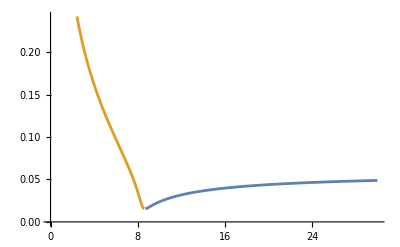

```mathematica
ListLinePlot[{ll2,rr2}]
```

```mathematica
ll2
```

{{0.1,First[{}]},{0.2,First[{}]},{0.3,First[{}]},{0.4,First[{}]},{0.5,First[{}]},{0.6,First[{}]},{0.7,First[{}]},{0.8,First[{}]},{0.9,First[{}]},{1.,First[{}]},{1.1,First[{}]},{1.2,First[{}]},{1.3,First[{}]},{1.4,First[{}]},{1.5,First[{}]},{1.6,First[{}]},{1.7,First[{}]},{1.8,First[{}]},{1.9,First[{}]},{2.,First[{}]},{2.1,First[{}]},{2.2,First[{}]},{2.3,First[{}]},{2.4,First[{}]},{2.5,First[{}]},{2.6,First[{}]},{2.7,First[{}]},{2.8,First[{}]},{2.9,First[{}]},{3.,First[{}]},{3.1,First[{}]},{3.2,First[{}]},{3.3,First[{}]},{3.4,First[{}]},{3.5,First[{}]},{3.6,First[{}]},{3.7,First[{}]},{3.8,First[{}]},{3.9,First[{}]},{4.,First[{}]},{4.1,First[{}]},{4.2,First[{}]},{4.3,First[{}]},{4.4,First[{}]},{4.5,First[{}]},{4.6,First[{}]},{4.7,First[{}]},{4.8,First[{}]},{4.9,First[{}]},{5.,First[{}]},{5.1,First[{}]},{5.2,First[{}]},{5.3,First[{}]},{5.4,First[{}]},{5.5,First[{}]},{5.6,First[{}]},{5.7,First[{}]},{5.8,First[{}]},{5.9,First[{}]},{6.,First[{}]},{6.1,First[{}]},{6.2,First[{}]},{6.3,First[{}]},{6.4,First[{}]},{6.5,First[{}]},{6.6,First[{}]},{6.7,First[{}]},{6.8,First[{}]},{6.9,First[{}]},{7.,First[{}]},{7.1,First[{}]},{7.2,First[{}]},{7.3,First[{}]},{7.4,First[{}]},{7.5,First[{}]},{7.6,First[{}]},{7.7,First[{}]},{7.8,First[{}]},{7.9,First[{}]},{8.,First[{}]},{8.1,First[{}]},{8.2,ϵ},{8.3,ϵ},{8.4,ϵ},{8.5,ϵ},{8.6,ϵ},{8.7,0.0154192},{8.8,0.0158075},{8.9,0.0164097},{9.,0.017106},{9.1,0.0178364},{9.2,0.0185709},{9.3,0.0192938},{9.4,0.0199977},{9.5,0.0206788},{9.6,0.0213359},{9.7,0.0219688},{9.8,0.0225779},{9.9,0.0231641},{10.,0.0237286},{10.1,0.0242722},{10.2,0.0247962},{10.3,0.0253016},{10.4,0.0257893},{10.5,0.0262604},{10.6,0.0267158},{10.7,0.0271563},{10.8,0.0275827},{10.9,0.0279957},{11.,0.028396},{11.1,0.0287843},{11.2,0.0291611},{11.3,0.029527},{11.4,0.0298825},{11.5,0.0302281},{11.6,0.0305642},{11.7,0.0308913},{11.8,0.0312098},{11.9,0.03152},{12.,0.0318223},{12.1,0.0321169},{12.2,0.0324043},{12.3,0.0326847},{12.4,0.0329584},{12.5,0.0332257},{12.6,0.0334867},{12.7,0.0337418},{12.8,0.033991},{12.9,0.0342348},{13.,0.0344732},{13.1,0.0347064},{13.2,0.0349346},{13.3,0.035158},{13.4,0.0353768},{13.5,0.035591},{13.6,0.0358009},{13.7,0.0360066},{13.8,0.0362082},{13.9,0.0364059},{14.,0.0365997},{14.1,0.0367898},{14.2,0.0369763},{14.3,0.0371594},{14.4,0.037339},{14.5,0.0375153},{14.6,0.0376885},{14.7,0.0378585},{14.8,0.0380255},{14.9,0.0381896},{15.,0.0383508},{15.1,0.0385093},{15.2,0.038665},{15.3,0.0388181},{15.4,0.0389687},{15.5,0.0391167},{15.6,0.0392623},{15.7,0.0394056},{15.8,0.0395466},{15.9,0.0396852},{16.,0.0398217},{16.1,0.0399561},{16.2,0.0400884},{16.3,0.0402186},{16.4,0.0403468},{16.5,0.0404731},{16.6,0.0405975},{16.7,0.0407201},{16.8,0.0408408},{16.9,0.0409598},{17.,0.041077},{17.1,0.0411925},{17.2,0.0413064},{17.3,0.0414187},{17.4,0.0415294},{17.5,0.0416385},{17.6,0.0417461},{17.7,0.0418523},{17.8,0.041957},{17.9,0.0420602},{18.,0.0421621},{18.1,0.0422626},{18.2,0.0423618},{18.3,0.0424597},{18.4,0.0425563},{18.5,0.0426516},{18.6,0.0427457},{18.7,0.0428386},{18.8,0.0429303},{18.9,0.0430209},{19.,0.0431103},{19.1,0.0431986},{19.2,0.0432858},{19.3,0.043372},{19.4,0.0434571},{19.5,0.0435411},{19.6,0.0436241},{19.7,0.0437062},{19.8,0.0437873},{19.9,0.0438674},{20.,0.0439465},{20.1,0.0440248},{20.2,0.0441021},{20.3,0.0441785},{20.4,0.0442541},{20.5,0.0443288},{20.6,0.0444026},{20.7,0.0444756},{20.8,0.0445478},{20.9,0.0446192},{21.,0.0446898},{21.1,0.0447597},{21.2,0.0448287},{21.3,0.044897},{21.4,0.0449646},{21.5,0.0450315},{21.6,0.0450976},{21.7,0.045163},{21.8,0.0452277},{21.9,0.0452918},{22.,0.0453552},{22.1,0.0454179},{22.2,0.04548},{22.3,0.0455414},{22.4,0.0456022},{22.5,0.0456624},{22.6,0.045722},{22.7,0.045781},{22.8,0.0458393},{22.9,0.0458971},{23.,0.0459544},{23.1,0.046011},{23.2,0.0460671},{23.3,0.0461227},{23.4,0.0461777},{23.5,0.0462322},{23.6,0.0462862},{23.7,0.0463396},{23.8,0.0463926},{23.9,0.046445},{24.,0.046497},{24.1,0.0465484},{24.2,0.0465994},{24.3,0.0466499},{24.4,0.0466999},{24.5,0.0467495},{24.6,0.0467986},{24.7,0.0468473},{24.8,0.0468955},{24.9,0.0469433},{25.,0.0469907},{25.1,0.0470376},{25.2,0.0470841},{25.3,0.0471302},{25.4,0.0471759},{25.5,0.0472212},{25.6,0.0472661},{25.7,0.0473107},{25.8,0.0473548},{25.9,0.0473985},{26.,0.0474419},{26.1,0.0474849},{26.2,0.0475275},{26.3,0.0475698},{26.4,0.0476117},{26.5,0.0476533},{26.6,0.0476945},{26.7,0.0477354},{26.8,0.0477759},{26.9,0.0478161},{27.,0.047856},{27.1,0.0478955},{27.2,0.0479347},{27.3,0.0479736},{27.4,0.0480122},{27.5,0.0480505},{27.6,0.0480884},{27.7,0.0481261},{27.8,0.0481635},{27.9,0.0482005},{28.,0.0482373},{28.1,0.0482738},{28.2,0.04831},{28.3,0.0483459},{28.4,0.0483815},{28.5,0.0484169},{28.6,0.048452},{28.7,0.0484868},{28.8,0.0485214},{28.9,0.0485556},{29.,0.0485897},{29.1,0.0486235},{29.2,0.048657},{29.3,0.0486902},{29.4,0.0487233},{29.5,0.048756},{29.6,0.0487886},{29.7,0.0488209},{29.8,0.0488529},{29.9,0.0488847},{30.,0.0489163}}

```mathematica
alph=0.95*Pi/2;
```

```mathematica
ohn=0.043;rho2=.14;rho1=0.86;mu1=0.71;mu2=0.29;alpha=alph;
```

```mathematica
b101[s_]:=bkl1fun[ohn,rho1,rho2,mu1,mu2,1,0,2,1,alpha]/.t->s;
b201[s_]:=bkl1fun[ohn,rho1,rho2,mu1,mu2,2,0,2,1,alpha]/.t->s;
b211[s_]:=c21*Cos[s]+d21*Sin[s]/.t->s;
b301[s_]:=bkl1fun[ohn,rho1,rho2,mu1,mu2,3,0,2,1,alpha]/.t->s;

etaa1[a_,b_,c_]:=b101[c]*realklpt[1,0,a,b]+b201[c]*realklpt[2,0,a,b]+b211[c]*realklpt[2,1,a,b]+b301[c]*realklpt[3,0,a,b]

fi11[rr_,a_,b_,c_]:=D[b101[c],c]/1*rr^1*realklpt[1,0,a,b]+D[b201[c],c]/2*rr^1*realklpt[2,0,a,b]+D[b211[c],c]/2*rr^2*realklpt[2,1,a,b]+D[b301[c],c]/3*rr^3*realklpt[3,0,a,b]

fi21[rr_,a_,b_,c_]:=-D[b101[c],c]/(2 rr^2)*realklpt[1,0,a,b]-D[b201[c],c]/(3 rr^2)*realklpt[2,0,a,b]-D[b211[c],c]/(3 rr^3)*realklpt[2,1,a,b]-D[b301[c],c]/(4 rr^4)*realklpt[3,0,a,b]

kkl1fun=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]]} //Chop;
lkl1fun=η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} ;
nkl1fun=1/We(-2 (η1[θ,φ,t]^2)+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))+rho1 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])-1/2 rho2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]};
```

```mathematica
alph
```

1.49226

```mathematica
Clear[b102f,b212f,b302f,k211f,k301f,etaa2,fi12,fi22,We]
ohn=0.043;rho2=.14;rho1=0.86;mu1=0.71;mu2=0.29;alpha=alph;
b102f[c_]:=bkl2fun[ohn,rho1,rho2,mu1,mu2,1,0,2,1,alpha]/.t->c;
b202f[c_]:=bkl2fun[ohn,rho1,rho2,mu1,mu2,2,0,2,1,alpha]/.t->c;
b212f[c_]:=bkl2fun[ohn,rho1,rho2,mu1,mu2,2,1,2,1,alpha]/.t->c;
b302f[c_]:=bkl2fun[ohn,rho1,rho2,mu1,mu2,3,0,2,1,alpha]/.t->c;
(*k201f[c_]:=k201ff/.t->c;*)
k101f[c_]:=kkl1fn[ohn,rho1,rho2,mu1,mu2,1,0,2,1,alpha]/.t->c;
k211f[c_]:=kkl1fn[ohn,rho1,rho2,mu1,mu2,2,1,2,1,alpha]/.t->c;
k301f[c_]:=kkl1fn[ohn,rho1,rho2,mu1,mu2,3,0,2,1,alpha]/.t->c;
(*l201f[c_]:=l201ff/.t->c;*)
l101f[c_]:=lkl1fn[ohn,rho1,rho2,mu1,mu2,1,0,2,1,alpha]/.t->c;
l211f[c_]:=lkl1fn[ohn,rho1,rho2,mu1,mu2,2,1,2,1,alpha]/.t->c;
l301f[c_]:=lkl1fn[ohn,rho1,rho2,mu1,mu2,3,0,2,1,alpha]/.t->c;

etaa2[a_,b_,c_]:=b102f[c]*realklpt[1,0,a,b]+b212f[c]*realklpt[2,1,a,b]+b302f[c]*realklpt[3,0,a,b];
fi12[rr_,a_,b_,c_]:=(D[b102f[c],c]+k101f[c])/1*rr^1*realklpt[1,0,a,b]+(D[b212f[c],c]+k211f[c])/2*rr^2*realklpt[2,1,a,b]+(D[b302f[c],c]+k301f[c])/3*rr^3*realklpt[3,0,a,b];
fi22[rr_,a_,b_,c_]:=-(D[b102f[c],c]+k101f[c]+l101f[c])/(2*rr^2)*realklpt[1,0,a,b]-(D[b212f[c],c]+k211f[c]+l211f[c])/(3*rr^3)*realklpt[2,1,a,b]-(D[b302f[c],c]+k301f[c]+l301f[c])/(4*rr^4)*realklpt[3,0,a,b];
```

```mathematica
kkl2fun=(-2 η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+Derivative[1,0,0][η2][θ,φ,t]) Derivative[0,1,0,0][ϕ11][1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] Derivative[0,1,0][η1][θ,φ,t]+Derivative[0,1,0][η2][θ,φ,t]) Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[0,1,0][η1][θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]};
nkl2fun=1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t])-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t]))+rho1 (η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])+rho2 (-η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} ;

lkl2fun=Csc[θ] Derivative[0,1,0][η1][θ,φ,t] (Csc[θ] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]-Csc[θ] Derivative[0,0,1,0][ϕ21][1,θ,φ,t])+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-Derivative[0,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]+η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]+1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]};
```

```mathematica
bkl3fun[0.043,0.86,0.14,0.71,0.29,2,1,2,1,alph]
```

{0.00715156,0.300646,-0.118225,-0.010622,π/2,-0.00506798,0.0201025,8.39161}

```mathematica
bkl3fun[0.043,0.86,0.14,0.71,0.29,2,1,2,1,alph]
```

{0.659149,-0.901317,-5.79126,0.656064,1.49226,-0.00506798,0.0201025,8.39161}

```mathematica
bkl3fun[0.043,0.86,0.14,0.71,0.29,2,1,2,1,alph]
```

{0.00715156,0.300646,-0.118225,-0.010622,π/2,-0.00506798,0.0201025,8.39161}

```mathematica
data
```

data

```mathematica
g1=0.0071515586996341775;g2=0.30064599833374195;
```

0.0119614

```mathematica
wem
```

8.39161

```mathematica
Δk
```

0.0201025

```mathematica
Δk=oh/wem(μ1*(k-1)+μ2*(k+2))*(k(k+1))/(ρ1(k+1)+ρ2*k)/.{oh->0.043,ρ1->0.86,ρ2->0.14,μ1->0.71,μ2->0.29}
```

0.0201025

```mathematica
epwe1[we_]:=Module[{sols},sols=ϵ/. Solve[zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ];
sols=Map[If[Abs[Im[#]]<10^-6,Re[#],#]&,sols];
sols=Select[sols,Element[#,Reals]&&#>0&];
First@sols]
```

```mathematica
epwe2[we_]:=Module[{sols},sols=ϵ/. Solve[zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ];
sols=Map[If[Abs[Im[#]]<10^-6,Re[#],#]&,sols];
sols=Select[sols,Element[#,Reals]&&#>0&];
First@sols]
```

```mathematica
ll2=Table[{we,epwe1[we]},{we,0.1,30,0.1}];
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[ϵ,#1∈&&#1>0&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

```mathematica
zetak
```

8.39161/we

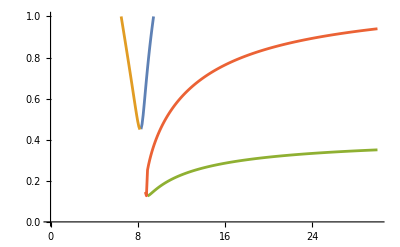

```mathematica
ListLinePlot[{ll,rr,ll2,rr2},PlotRange->{{0,30},{0,1}}]
```

```mathematica
Integrate[realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

-(√(7 π))/8

```mathematica
(√(Pi*(2*3+1)))/7*(LegendreP[2,0]-LegendreP[4,0])
```

-(√(7 π))/8

```mathematica
Series[Cos[e*x],{e,0,2}]
```

1-(x^2 e^2)/2+O[e]^3

```mathematica
Series[HeavisideTheta[Cos[th]-1+e*Cos[t]],{e,0,3}]
```

HeavisideTheta[-1+Cos[th]]+O[e]^4

```mathematica
Asymptotic[HeavisideTheta[Cos[th]-1+e Cos[t]],{e,0,∞}]
```

HeavisideTheta[-1+e Cos[t]+Cos[th]]

```mathematica
Integrate[realklpt[3,0,θ,φ]*Sin[θ],{θ,0,alp},{φ,0,2Pi}]//FullSimplify
```

1/16 √(7 π) (3+5 Cos[2 alp]) Sin[alp]^2

```mathematica
Integrate[realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi/5},{φ,0,2Pi}]//FullSimplify
```

0

```mathematica
DSolve[{z''[t]+d*z'[t]+c*z[t]==-g,z[0]==0,z'[0]==0},z[t],t]//FullSimplify
```

{{z[t]→(ⅇ^(-1/2 (d+√(-4 c+d^2)) t) (d (-1+ⅇ^(√(-4 c+d^2) t))+√(-4 c+d^2) (1+ⅇ^(√(-4 c+d^2) t)-2 ⅇ^(1/2 (d+√(-4 c+d^2)) t))) g)/(2 c √(-4 c+d^2))}}

```mathematica
(ⅇ^(-1/2 (d+√(-4 c+d^2)) t) (d (-1+ⅇ^(√(-4 c+d^2) t))+√(-4 c+d^2) (1+ⅇ^(√(-4 c+d^2) t)-2 ⅇ^(1/2 (d+√(-4 c+d^2)) t))) g)/(2 c √(-4 c+d^2))/.{g->9.8,d->0.01,c->1}
```

(0.-2.45003 ⅈ) ⅇ^((-0.005-0.999987 ⅈ) t) (0.01 (-1+ⅇ^((0.+1.99997 ⅈ) t))+(0.+1.99997 ⅈ) (1+ⅇ^((0.+1.99997 ⅈ) t)-2 ⅇ^((0.005+0.999987 ⅈ) t)))

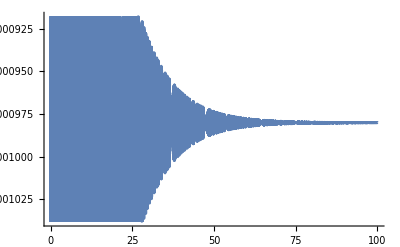

```mathematica
Plot[(ⅇ^(-1/2 (d+√(-4 c+d^2)) t) (d (-1+ⅇ^(√(-4 c+d^2) t))+√(-4 c+d^2) (1+ⅇ^(√(-4 c+d^2) t)-2 ⅇ^(1/2 (d+√(-4 c+d^2)) t))) g)/(2 c √(-4 c+d^2))/.{g->9.8,d->0.2,c->10000},{t,0,100}]
```

```mathematica
Series[Cos[x],{x,0,3}]
```

1-x^2/2+O[x]^4

```mathematica
a=1;Integrate[realklpt[2,1,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[2,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[1,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[3,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
```

0

0

(√(3 π))/2

-(√(7 π))/8

```mathematica
a=0.99;Integrate[realklpt[2,1,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[2,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[1,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[3,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[4,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
```

0

0.0311189

1.53461

-0.585316

-0.0312948

```mathematica
a=0.49;Integrate[realklpt[2,1,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[2,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[1,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[3,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
Integrate[realklpt[4,0,θ,φ]*Sin[θ],{θ,0,a*Pi/2},{φ,0,2Pi}]
```

0

0.689192

0.743387

0.448121

0.140994

```mathematica
LegendreP[2,Cos[θ]]
```

1/2 (-1+3 Cos[θ]^2)

```mathematica
LegendreP[k,1]
```

1

```mathematica
Series[LegendreP[2,1-e],{e,0,2}]
```

1-3 e+(3 e^2)/2+O[e]^3

```mathematica
Series[LegendreP[4,1-e],{e,0,2}]
```

1-10 e+(45 e^2)/2+O[e]^3

```mathematica
Series[LegendreP[k,1-e],{e,0,2}]//FullSimplify
```

1-1/2 (k (1+k)) e+1/16 (-1+k) k (1+k) (2+k) e^2+O[e]^3

```mathematica
(-1+k) k (1+k) (2+k)/.{k->l+1}
```

l (1+l) (2+l) (3+l)

```mathematica
(-1+k) k (1+k) (2+k)/.{k->l-1}
```

(-2+l) (-1+l) l (1+l)

```mathematica
(-2+l) (-1+l) l (1+l)-l (1+l) (2+l) (3+l)//FullSimplify
```

-4 l (1+l) (1+2 l)

```mathematica
(1-Cos[2*ω*t])^2//TrigReduce
```

1/2 (3-4 Cos[2 t ω]+Cos[4 t ω])